```mathematica
(*************************  NIPOTI  ************************)

Manipulate[
coloreDenominatore = Blue;
coloreNumeratore = Red;
spaceX = 6.5;
objNipoti = {};    (* oggetto che contiene la lista degli oggetti grafici che compongono il singolo nipote (line, line, circle etc.)*)
plotRange = 15;
offsetX = -19;
offsetY = 3;
For[i = 0, i< numeroNipoti,i++,
AppendTo[objNipoti,
{Thickness[.01],
Line[{{0 + (i*spaceX)+offsetX,0},{2 + (i*spaceX)+offsetX,3}}],(*Gamba destra*)
Line[{{2 + (i*spaceX)+offsetX,3},{4 + (i*spaceX)+offsetX,0}}],(*Gamba sinistra*)
Line[{{2 + (i*spaceX)+offsetX,3},{2 + (i*spaceX)+offsetX,7}}], (*Busto*)
Line[{{2 + (i*spaceX)+offsetX,7},{4 + (i*spaceX)+offsetX,5}}], (* Braccio destro*)
Line[{{2 + (i*spaceX)+offsetX,7},{0 + (i*spaceX)+offsetX,5}}], (* Braccio sinistro*)

Circle[{2 + (i*spaceX)+offsetX,8.5},1.4]

}]
(*{Black,Rectangle[{(i*spaceX)+offsetX,0},{3+(i*spaceX)+ offsetX,6}], Disk[{1.5+ (i*spaceX)+offsetX, 6}, 1.5], Black, Rectangle[{1+(i*spaceX)+offsetX,7},{2+ (i*spaceX)+offsetX,9}]}}*)
];
objBicchieri = {};
offsetX = -9;
offsetY = -6;
(* For[i = 0, i< numeroBicchieri,i++,
AppendTo[objBicchieri,{Black,Circle[{(i*2)+offsetX,0 + offsetY},1]}]
]; *)
Graphics[{
objNipoti,
objBicchieri
},PlotRange->{{-20,40},{-15,15}}]
(*paramentri primo slider*)
,{
{numeroNipoti,1,(*valore iniziale slider numeratore*)
		Style["Numero Nipoti",Directive[coloreNumeratore,Large]]},
	1,8,1,(*valore iniziale, valore finale, step di incremento/decremento slider*)
	Appearance->{"Labeled"},
	AppearanceElements->{"InputField"},
	LabelStyle->Directive[coloreNumeratore,Large],
	ImageSize->170
	}(*,(*--fine slider numeratore*)
{
{numeroBicchieri,2,Style["Numero bicchieri",Directive[coloreDenominatore,Large]]}
,1,10,1,
	Appearance->{"Labeled"},
	AppearanceElements->{"InputField"},(*rimuovo tutto tranne l'inputField*)
	LabelStyle->Directive[coloreDenominatore,Large],ImageSize->170}*)
]
```

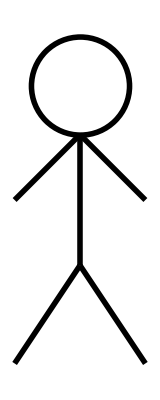

```mathematica
Graphics[{Thickness[.01],
Line[{{0,0},{2,3}}],(*Gamba destra*)
Line[{{2,3},{4,0}}],(*Gamba sinistra*)
Line[{{2,3},{2,7}}], (*Busto*)
Line[{{2,7},{0,5}}],
Line[{{2,7},{4,5}}],
Circle[{2,8.5},1.5]

}, PlotRange-> Automatic]
```

```mathematica
(* MONETE NIPOTI *)
Manipulate[
coloreNumeratore = Red;
spaceX = 4.5;
spaceXMonete = 60;
objNipoti = {};    (* oggetto che contiene la lista degli oggetti grafici che compongono il singolo nipote (line, line, circle etc.)*)
objMonete = {};
offsetX = -15;
offsetY = -4;
offsetX2 = -400;
offsetY2 = -150;
raggio1 = 32;   (* Per modificare la grandezza delle monete -> modificare raggio1 , raggio2 e FontSize nello Style*)
raggio2 = 42;
For[i = 0, i< numeroMonete,i++,
AppendTo[objNipoti,{Thick,Yellow,EdgeForm[{Thick, Black}], Disk[{0 +(i*spaceXMonete) + offsetX2,0 +offsetY2}, raggio2],Thick,Yellow,EdgeForm[{Thick, Black}], Disk[{0 +(i*spaceXMonete) + offsetX2,0 +offsetY2},raggio1],Text[Style["$",Large,Bold, Black, Thick, FontSize->30], {0 + (i*spaceXMonete) + offsetX2,0 + offsetY2 },Automatic ]}]
(*{Black,Rectangle[{(i*spaceX)+offsetX,0},{3+(i*spaceX)+ offsetX,6}], Disk[{1.5+ (i*spaceX)+offsetX, 6}, 1.5], Black, Rectangle[{1+(i*spaceX)+offsetX,7},{2+ (i*spaceX)+offsetX,9}]}}*)
];
objBicchieri = {};
offsetX = -9;
offsetY = -6;
(* For[i = 0, i< numeroBicchieri,i++,
AppendTo[objBicchieri,{Black,Circle[{(i*2)+offsetX,0 + offsetY},1]}]
]; *)
Graphics[{
objNipoti,
objMonete
},ImageSize->{800, 500}, PlotRange->{{-600,600},{-500,500}}]
(*paramentri primo slider*)
,{
{numeroMonete,3,(*valore iniziale slider numeratore*)
		Style["Numero Monete",Directive[coloreNumeratore,Large]]},
	3,30,3,(*valore iniziale, valore finale, step di incremento/decremento slider*)
	Appearance->{"Labeled"},
	AppearanceElements->{"InputField"},
	LabelStyle->Directive[coloreNumeratore,Large],
	ImageSize->170
	}(*,(*--fine slider numeratore*)
{
{numeroBicchieri,2,Style["Numero bicchieri",Directive[coloreDenominatore,Large]]}
,1,10,1,
	Appearance->{"Labeled"},
	AppearanceElements->{"InputField"},(*rimuovo tutto tranne l'inputField*)
	LabelStyle->Directive[coloreDenominatore,Large],ImageSize->170}*)
]
```

```mathematica
graphi
```